## Tasks

1) get critical congestion code working (association) (DONE??)
2) post-processing : plots u, currents, m, ... (DONE??)
	answers simple questions: boundary conditions, (what are the questions?)

```mathematica
Names["MFGraphs`*"]
```

{a,A,alpha,AtHead,AtTail,a$,beta,DataG,DataToEquations,edge,edge$,EqEliminatorX,F,FixedReduceX1,g,H,I1,I2,Intg,IntM,j,j$,m,M,n,NewReduce,OtherWay,p,p$,S1,S10,S11,S12,S13,S14,S15,S16,S2,S3,S4,S5,S6,S7,S8,S9,SortAnds,test,TransitionsAt,triple2path,U,U1,U2,U3,V,W,x,xi,y,ZAnd}

```mathematica
Get["MFGraphs`Examples`ExamplesData`"]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,3,2,S1}}|>

DataToEquations: Triangle inequalities for switching costs: {True}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce the critical congestion case with NewReduce!
The system is True

DataToEquations: Critical congestion solved.

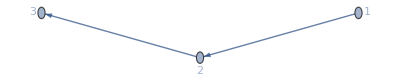
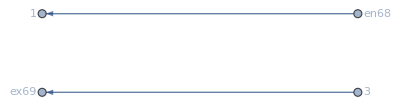
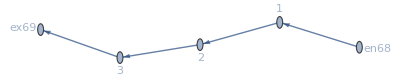
<|BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en68|>,InEdges→{en68->1},ExitVertices→{3},OutwardVertices→<|3→ex69|>,OutEdges→{3->ex69},AuxiliaryGraph→-Graphics-,FG→-Graphics-,VL→{1,2,3},EL→{1->2,2->3,3->ex69,en68->1},BEL→{1->2,2->3},FVL→{1,2,3,en68,ex69},AllTransitions→{{1,1->2,en68->1},{1,en68->1,1->2},{2,1->2,2->3},{2,2->3,1->2},{3,2->3,3->ex69},{3,3->ex69,2->3}},NoDeadEnds→{{1,1->2},{1,en68->1},{2,1->2},{2,2->3},{3,2->3},{3,3->ex69}},NoDeadStarts→{{2,1->2},{en68,en68->1},{1,1->2},{3,2->3},{2,2->3},{ex69,3->ex69}},jargs→{{2,1->2},{3,2->3},{ex69,3->ex69},{1,en68->1},{1,1->2},{2,2->3},{3,3->ex69},{en68,en68->1}},js→{j70,j71,j72,j73,j74,j75,j76,j77},jvars→<|{2,1->2}→j70,{3,2->3}→j71,{ex69,3->ex69}→j72,{1,en68->1}→j73,{1,1->2}→j74,{2,2->3}→j75,{3,3->ex69}→j76,{en68,en68->1}→j77|>,jts→{jt78,jt79,jt80,jt81,jt82,jt83},jtvars→<|{1,1->2,en68->1}→jt78,{1,en68->1,1->2}→jt79,{2,1->2,2->3}→jt80,{2,2->3,1->2}→jt81,{3,2->3,3->ex69}→jt82,{3,3->ex69,2->3}→jt83|>,uargs→{{1,1->2},{2,2->3},{3,3->ex69},{en68,en68->1},{2,1->2},{3,2->3},{ex69,3->ex69},{1,en68->1}},us→{u84,u85,u86,u87,u88,u89,u90,u91},uvars→<|{1,1->2}→u84,{2,2->3}→u85,{3,3->ex69}→u86,{en68,en68->1}→u87,{2,1->2}→u88,{3,2->3}→u89,{ex69,3->ex69}→u90,{1,en68->1}→u91|>,SwitchingCosts→<|{1,1->2,en68->1}→∞,{1,en68->1,1->2}→0,{2,1->2,2->3}→0,{2,2->3,1->2}→0,{3,2->3,3->ex69}→0,{3,3->ex69,2->3}→∞,
There is no path from 1 to 3 to 2→2,{3,3->ex69,1->2}→∞,{3,3->ex69,3->ex69}→∞,{3,3->ex69,en68->1}→∞,{1,en68->1,en68->1}→∞|>,OutRules→{{3,3->ex69,1->2}→∞,{3,3->ex69,2->3}→∞,{3,3->ex69,3->ex69}→∞,{3,3->ex69,en68->1}→∞},InRules→{{1,1->2,en68->1}→∞,{1,en68->1,en68->1}→∞},EntryArgs→{{1,en68->1}},EntryDataAssociation→<|{1,en68->1}→2|>,jays→<|1->2→j70-j74,2->3→j71-j75|>,NonZeroEntryCurrents→True,ExitCosts→<|ex69→0|>,EqCurrentCompCon→(j74==0||j70==0)&&(j75==0||j71==0)&&(j76==0||j72==0)&&(j77==0||j73==0),EqTransitionCompCon→(jt78==0||jt79==0)&&(jt80==0||jt81==0)&&(jt82==0||jt83==0),EqCompCon→jt78==0&&(jt79==0||u84-u91==0)&&(jt80==0||u85-u88==0)&&(jt81==0||-u85+u88==0)&&(jt82==0||u86-u89==0)&&jt83==0,EqAllComp→(j74==0||j70==0)&&(j75==0||j71==0)&&(j76==0||j72==0)&&(j77==0||j73==0)&&(jt78==0||jt79==0)&&(jt80==0||jt81==0)&&(jt82==0||jt83==0)&&jt78==0&&(jt79==0||u84-u91==0)&&(jt80==0||u85-u88==0)&&(jt81==0||-u85+u88==0)&&(jt82==0||u86-u89==0)&&jt83==0,EqPosCon→NonNegative[j70]&&NonNegative[j71]&&NonNegative[j72]&&NonNegative[j73]&&NonNegative[j74]&&NonNegative[j75]&&NonNegative[j76]&&NonNegative[j77]&&NonNegative[jt78]&&NonNegative[jt79]&&NonNegative[jt80]&&NonNegative[jt81]&&NonNegative[jt82]&&NonNegative[jt83],EqBalanceSplittingCurrents→j74==jt78&&j73==jt79&&j70==jt80&&j75==jt81&&j71==jt82&&j76==jt83,EqBalanceGatheringCurrents→j70==jt79&&j77==jt78&&j74==jt81&&j71==jt80&&j75==jt83&&j72==jt82,EqEntryIn→j73==2,EqExitValues→u90==0,EqSwitchingConditions→u84≥u91&&u85==u88&&u86≥u89,EqValueAuxiliaryEdges→-u87+u91==0&&-u86+u90==0,EqAll→NonNegative[j70]&&NonNegative[j71]&&NonNegative[j72]&&NonNegative[j73]&&NonNegative[j74]&&NonNegative[j75]&&NonNegative[j76]&&NonNegative[j77]&&NonNegative[jt78]&&NonNegative[jt79]&&NonNegative[jt80]&&NonNegative[jt81]&&NonNegative[jt82]&&NonNegative[jt83]&&j74==jt78&&j73==jt79&&j70==jt80&&j75==jt81&&j71==jt82&&j76==jt83&&j70==jt79&&j77==jt78&&j74==jt81&&j71==jt80&&j75==jt83&&j72==jt82&&j73==2&&u90==0&&u84≥u91&&u85==u88&&u86≥u89&&-u87+u91==0&&-u86+u90==0,EqAllAll→NonNegative[j70]&&NonNegative[j71]&&NonNegative[j72]&&NonNegative[j73]&&NonNegative[j74]&&NonNegative[j75]&&NonNegative[j76]&&NonNegative[j77]&&NonNegative[jt78]&&NonNegative[jt79]&&NonNegative[jt80]&&NonNegative[jt81]&&NonNegative[jt82]&&NonNegative[jt83]&&j74==jt78&&j73==jt79&&j70==jt80&&j75==jt81&&j71==jt82&&j76==jt83&&j70==jt79&&j77==jt78&&j74==jt81&&j71==jt80&&j75==jt83&&j72==jt82&&j73==2&&u90==0&&u84≥u91&&u85==u88&&u86≥u89&&-u87+u91==0&&-u86+u90==0&&(j74==0||j70==0)&&(j75==0||j71==0)&&(j76==0||j72==0)&&(j77==0||j73==0)&&(jt78==0||jt79==0)&&(jt80==0||jt81==0)&&(jt82==0||jt83==0)&&jt78==0&&(jt79==0||u84-u91==0)&&(jt80==0||u85-u88==0)&&(jt81==0||-u85+u88==0)&&(jt82==0||u86-u89==0)&&jt83==0,BoundaryRules→{j73→2,u90→0},RulesEntryIn→{j73→2},RulesExitValues→{u90→0},Nlhs→{j70-j74-u84+u88,j71-j75-u85+u89},MinimalTimeRhs→{0,0},EqCriticalCase→j70-j74-u84+u88==0&&j71-j75-u85+u89==0,criticalreduced1→{True,<|j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,jt78→0,jt79→2,jt80→2,jt81→0,jt82→2,jt83→0,u84→4,u86→0,u88→2,u89→0,u90→0,u91→4,u85→2,u87→4|>},Nrhs→{j70-j74+IntM[j70-j74,1->2],j71-j75+IntM[j71-j75,2->3]},EqGeneralCase→j70-j74-u84+u88==j70-j74+IntM[j70-j74,1->2]&&j71-j75-u85+u89==j71-j75+IntM[j71-j75,2->3],TOL→1/1000000|>

```mathematica
n=16;
Data = DataG[n]
MFGEquations=DataToEquations[Data/.{U1->0,I1->2,S1->2}]
```